## QWZ Model

## 1.Bulk Dispersion and Graphical way of Chern Number

### 1.1 Bulk Dispersion

```mathematica
Clear["Global`*"]
bulkHamiltonian[kx_,ky_]:=Module[{dx,dy,dz},
dx=Sin[kx];dy=Sin[ky];dz=u+Cos[kx]+Cos[ky];
ham=Dot[{dx,dy,dz},Table[PauliMatrix[i],{i,1,3}]];
Return[ham]
]
hk=bulkHamiltonian[kx,ky]//Normal;
```

```mathematica
el=Sort@Eigenvalues[hk]
```

{-√(2+u^2+2 u Cos[kx]+Cos[kx-ky]+2 u Cos[ky]+Cos[kx+ky]),√(2+u^2+2 u Cos[kx]+Cos[kx-ky]+2 u Cos[ky]+Cos[kx+ky])}

```mathematica
Partition[Table[Plot3D[Evaluate[el/.{u->u0}],{kx,-π,π},{ky,-π,π},
Mesh->None,ColorFunction->"RedGreenSplit",AxesLabel->{kx,ky,Energy},Ticks->{{-π,0,π},{-π,0,π},{-2,0,2}},BoxRatios->{1, 1, 1.5},BoundaryStyle->None,PlotStyle->Opacity[0.75]],
{u0,{-2,0,2,-1.8}}],2]//Grid
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

### 1.2 Graphic Chern number

We simply count how many times the torus of BZ d contains the origin. The corresponding d vector reads,
								d(k_x,k_y)=(sin k_x
sin k_y
u+cos k_x+cosk_y)
to get some feeling about the not so trivial geometry of the torus, it is instructive to follow a gradual sweep of the Brillouin zone. The parameter  shifts the whole torus along the  direction, thus as we tune it we also control whether the origin is contained inside it or not.

```mathematica
Grid@Transpose@Partition[Show[#,Graphics3D[{PointSize[Large],Red,Point[{0,0,0}]}]]&/@Table[ParametricPlot3D[{Sin[x],Sin[y],u+Cos[x]+Cos[y]}/.{u->u0},{x,-π,π},{y,-π,0},Mesh->None,ViewPoint->{1.3, 1.4, 0.5},ColorFunction->"BlueGreenYellow",PerformanceGoal->"Quality",Boxed->True,Axes->False],{u0,{-2.2,-1,1,2.2}}],1]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

#### 画⚪的tricks

```mathematica
With[{m = 4, r = 1, h = 0.8}, 
Show[Graphics3D[Point[(Append[#1, 0] & ) /@ 
    CirclePoints[105]]], ParametricPlot3D[
  {r*Cos[ϕ], r*Sin[ϕ], h*Sin[m*ϕ]}, {ϕ, 0, 2*Pi}, 
  PlotStyle -> Tube[0.03], Axes -> False, 
  BoundaryStyle -> None, PlotRange -> 
   1.1*{{-r, r}, {-r, r}, {-h, h}}], Boxed -> False, 
 ImageSize -> 120]]
```

-Graphics3D-

### 1.3 The Ribbon Band

The bulk Hamiltonian reads,

```mathematica
Grid@Dot[{Sin[kx],Sin[ky],u+Cos[kx]+Cos[ky]},Table[PauliMatrix[i],{i,1,3}]]
```

u+Cos[kx]+Cos[ky] | Sin[kx]-ⅈ Sin[ky]
Sin[kx]+ⅈ Sin[ky] | -u-Cos[kx]-Cos[ky]

The real space image with  periodical.

```mathematica
Clear["Global`*"];
hamiltonian[ky_,num_]:=Module[{ham,h00,h01,sx,sy,sz},
Thread[{sx,sy,sz}=Table[PauliMatrix[i],{i,1,3}]];
h00=KroneckerProduct[DiagonalMatrix[Table[1,num-1],1],(sz+ⅈ sx)/2]+KroneckerProduct[DiagonalMatrix[Table[1,num-1],-1],(sz-ⅈ sx)/2];
h01=KroneckerProduct[DiagonalMatrix[Table[1,num]],Cos[ky] sz+Sin[ky]sy+u sz];
ham=h00+h01;
Return[ham]
]
hk=hamiltonian[ky,20]//Normal;
el=ParallelTable[Sort@Eigenvalues[N[hk/.{ky->kk,u->-1.5}]],{kk,-π,π,0.01*π}];
```

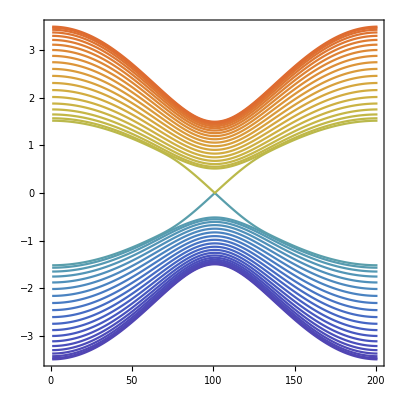

```mathematica
ListPlot[Transpose@Re[el],PlotRange->All,Joined->True,AspectRatio->1,Frame->True,ColorFunction->"Rainbow"]
```

```mathematica
Clear["Global`*"];
hamiltonian[ky_,num_]:=Module[{ham,h00,h01,ht,sx,sy,sz},
Thread[{sx,sy,sz}=Table[PauliMatrix[i],{i,1,3}]];
h00=KroneckerProduct[DiagonalMatrix[Table[1,num-1],1],(sz+ⅈ sx)/2]+KroneckerProduct[DiagonalMatrix[Table[1,num-1],-1],(sz-ⅈ sx)/2];
h01=KroneckerProduct[DiagonalMatrix[Table[1,num]],Cos[ky] sz+Sin[ky]sy+u sz];
ht=KroneckerProduct[Normal[SparseArray[{num,num}->1,num]],h*Cos[2 ky] IdentityMatrix[2]]+KroneckerProduct[Normal[SparseArray[{1,1}->1,num]],μ IdentityMatrix[2]];
ham=h00+h01+ht;
Return[ham]
]
hk=hamiltonian[ky,20]//Normal;
el1=ParallelTable[Sort@Eigenvalues[N[hk/.{ky->kk,u->-1.2,h->2,μ->0.5}]],{kk,-π,π,0.01*π}];
el2=ParallelTable[Sort@Eigenvalues[N[hk/.{ky->kk,u->-1.2,h->2,μ->6}]],{kk,-π,π,0.01*π}];
```

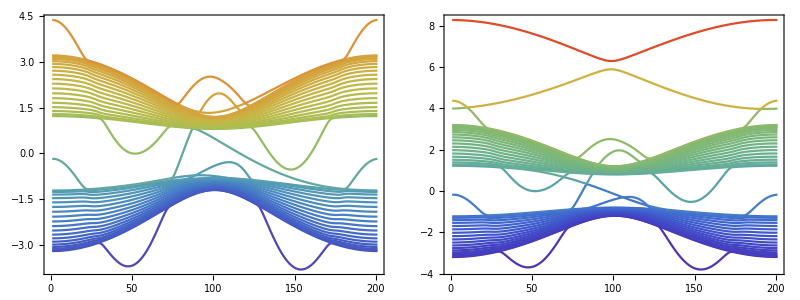

```mathematica
Grid@Transpose@Partition[#,1]&@{ListPlot[Transpose@Re[el1],PlotRange->All,Joined->True,AspectRatio->1,Frame->True,ColorFunction->"Rainbow"],ListPlot[Transpose@Re[el2],PlotRange->All,Joined->True,AspectRatio->1,Frame->True,ColorFunction->"Rainbow"]}
```